A Minimal Model for Biodiversity

Willem Nielsen

If I were to imagine the way to study say bacteria from the ground up, I would think about getting a microscope, finding ways to measure concentrations, figure out how to do DNA testing etc etc. 

What I would never in a million years suggest, is to boot up Mathematica, start running these so-called simple programs, use these bizarre arrays of multi-colored boxes to view the results, try to then figure out the behavior of these programs, and then somehow relate their behavior to bacteria. At first glance, this is an utterly ridiculous idea and one that I actively resisted myself. 

But doing science this ass-backwards way actually works, and works well at that. To convince yourself of this it requires a whole book and that’s what New Kind of Science aims to do. In a sentence, it’s because computation is all there is. There is no super-computation out in the world that cannot, in principle, be captured by our computers. And, there actually are broad laws that can be derived from studying these simple programs, such as the principal of computational equivalence. 

One big upside of starting with the abstract and then going to the concrete, as New Kind of Science suggests, is that you can learn about many subjects in one. You effectively get a lot of bang for your buck.

In the past, the main language of science was mathematics. My trouble with mathematics comes from the high overhead cost in understanding what the hell is going on within an equation. Using computational diagrams doesn’t have this problem, and the right diagram can provide instantaneous understanding. 

To be clear, I don’t think NKS is going to answer the questions that have stumped biologists for decades. I do believe though, that it is going to help pose and answer new questions. 

For me, a noisy metric for learning is how much fun I’m having. And because of the combination highlighted above, I’m having an absolute ball doing NKS, which, to me, is strong evidence for its power as an approach to science. 

Hopefully, that gives you some background for why I’m doing this. We’re now going to try to tackle the question of biodiversity. 

I’m shocked that someone has not done the experiments with cellular automata that Wolfram recently did regarding evolution. He said himself he could’ve, in principle, done that experiment forty years ago. But, science seems to only make sense looking backward. Because of this, I believe there are many discoveries to be made in the world of NKS for biology and that’s why I’m doing this research.

So in his article Wolfram mainly focuses on the programs go from short to long and therefore, from simple to complex. In an attempt to model bacterial resistance, I examined another dimension, that of diversity. One approach is to start with a rule and then explicitly look for “new ideas”. That is, look for automata with the pattern that is most different from any of its predecessors, judged by difference in corresponding boxes.

So we start with this rule here.

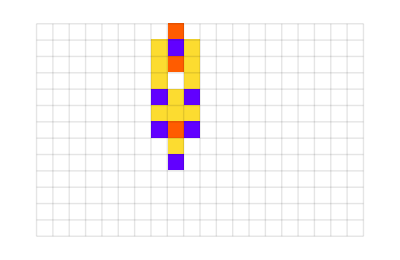

```mathematica
plot@trirule
```

Then we generate a bunch of random mutations and select only ones that are about the same length. Of those, we select the one that is most different from the previous automata. In this case, this was the most different.

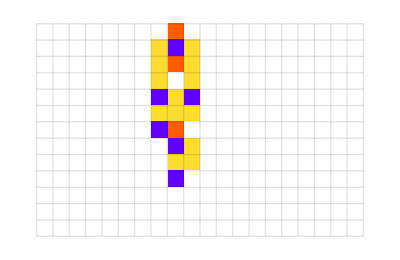

```mathematica
plot[ getmostdiff[{trirule}][[-1]]]
```

We do this recursively and basically ask the question, how different can we get? In some cases we don’t make it very far.

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]];
```

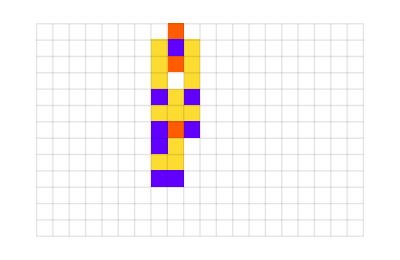
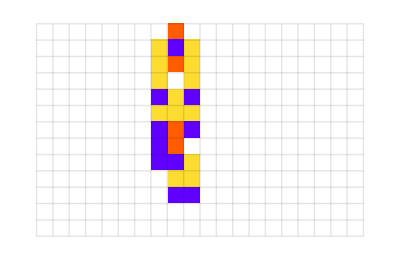
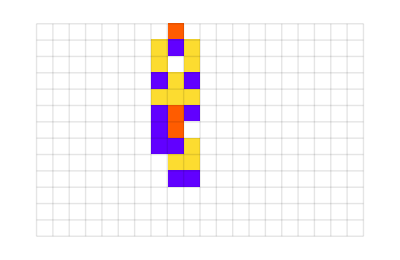
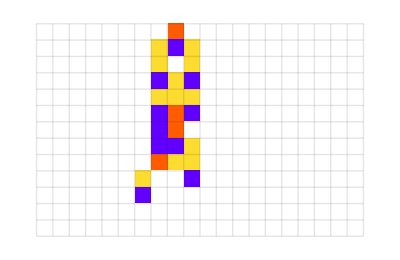
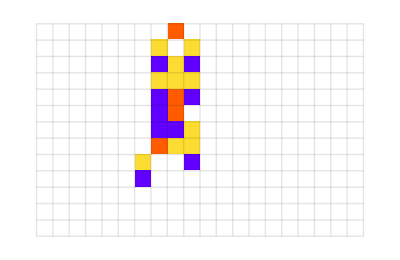
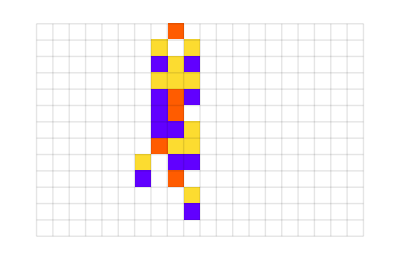
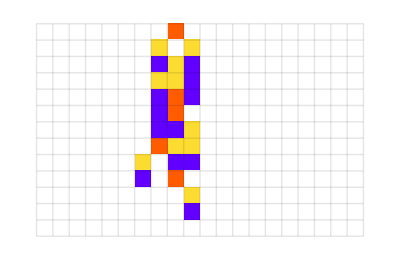
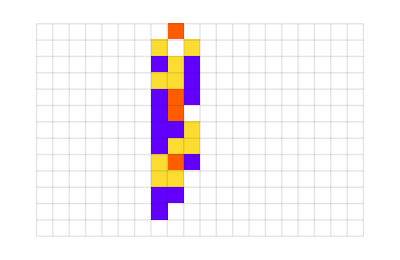
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@diffsmemo[[-1]]
```

```mathematica
Partition[{1, 2, 3, 4, 5, 6, 7}, 2, 1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7}}

```mathematica
pairs = Partition[diffsmemo[[3]], 2, 1];
```

```mathematica
pairs = Partition[diffsmemo[[3]], 2, 1];
```

```mathematica
f@@@{{a, b}, {b, c}}
```

{f[a,b],f[b,c]}

```mathematica
diffamounts = getdiffrule@@@pairs;
```

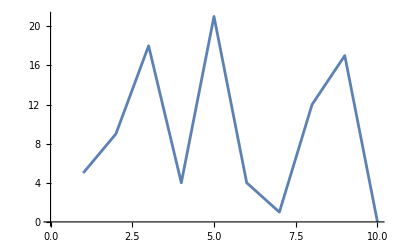

```mathematica
ListLinePlot[diffamounts]
```

In some cases we have one radical new idea.

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 20]];
```

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

General::stop: Further output of TakeLargestBy::insuff will be suppressed during this calculation.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

General::stop: Further output of CellularAutomaton::rlist will be suppressed during this calculation.

AppendTo::rvalue: diffsmemo is not a variable with a value, so its value cannot be changed.

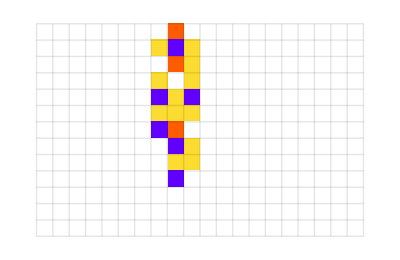
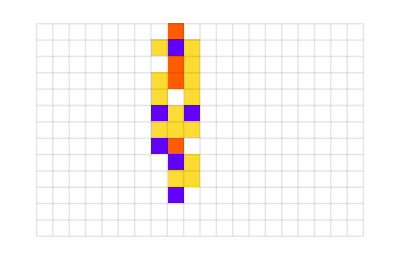
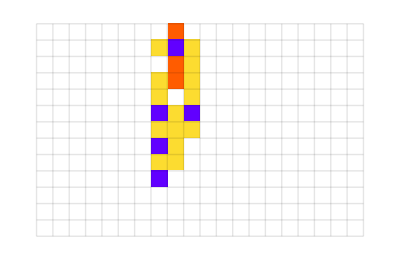
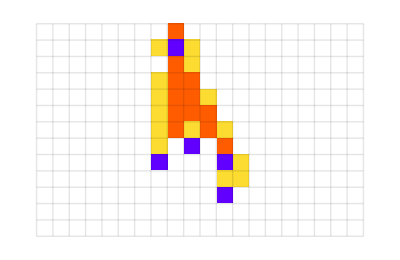
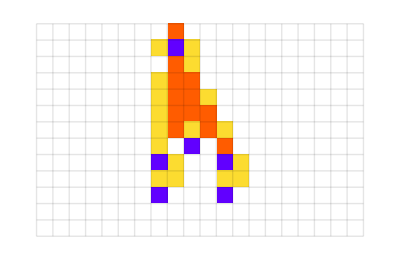
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@diffsmemo[[-1]]
```

In some cases we get stuck.

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]];
```

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

General::stop: Further output of CellularAutomaton::nspecnl will be suppressed during this calculation.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

General::stop: Further output of CellularAutomaton::kspec will be suppressed during this calculation.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

General::stop: Further output of TakeLargestBy::insuff will be suppressed during this calculation.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

General::stop: Further output of CellularAutomaton::rlist will be suppressed during this calculation.

```mathematica
plot/@diffsmemo[[-1]]
```

{-Graphics-,plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}],plot[{}]}

In some cases, we have an explosion of new ideas.

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]];
```

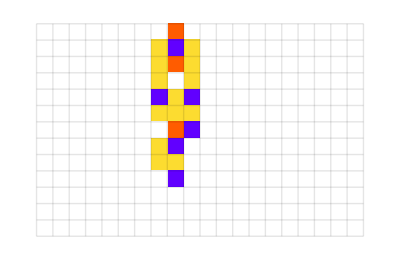
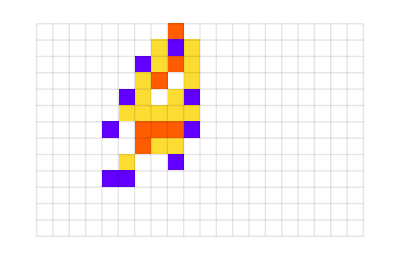
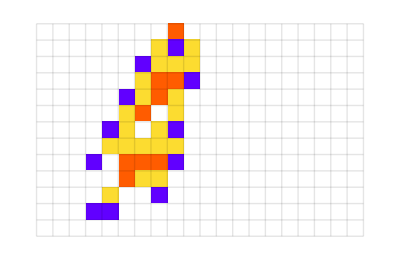
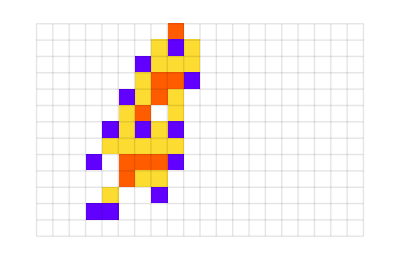
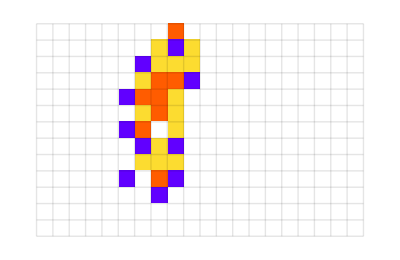
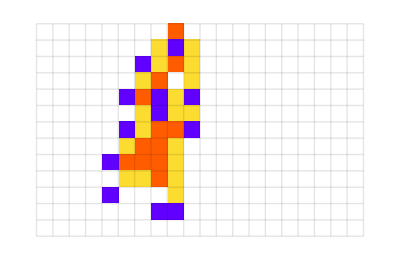
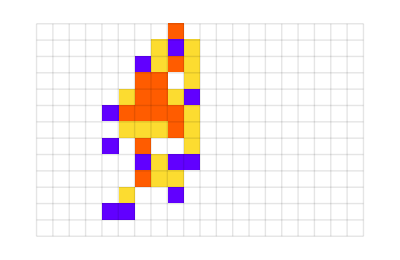
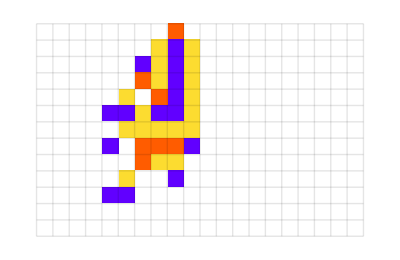
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plot/@diffsmemo[[-1]]
```

So my idea here, is to examine what Wolfram calls “fitness-neutral” sets. We start with k = 2, r = 3/2 because the multiway graph is manageable.

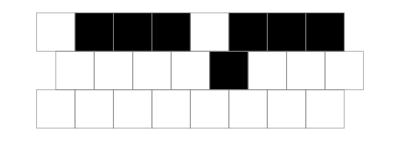
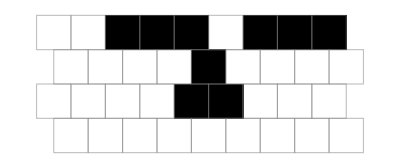
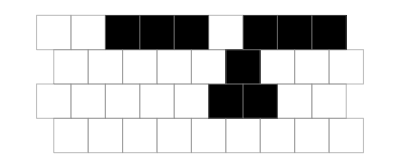
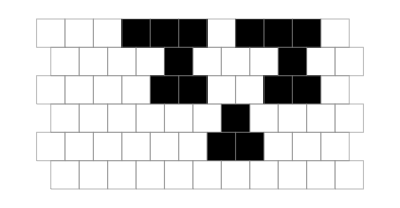
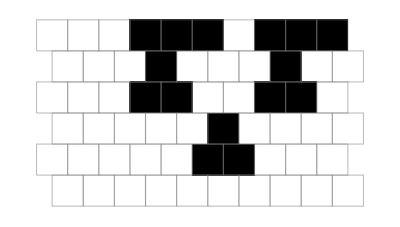
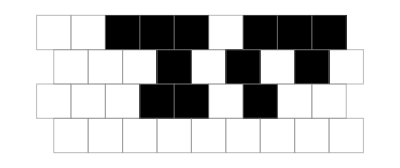
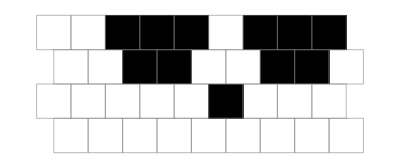
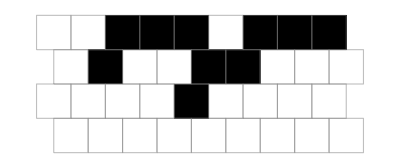

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

And here are some examples of various fitness-neutral sets.

```mathematica
Module[{mg,res,sublevels,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
sublevels=Map[Subgraph[mg,#]&,sublevels];
sublevels=Lookup[sublevels,{{3,6},{3,5},{6,7},{7,1}}];
Graph[#,
VertexSize->1/2,PerformanceGoal->"Quality",
EdgeStyle->Gray,ImageSize->{UpTo[350],200},
VertexShapeFunction->Function[
Inset[{{"[◼]", "SerratedBricksArrayPlot"}}[
CellularAutomaton[{#2,2,3/2},
{{1,1,1,0,1,1,1},0},
{{"[◼]", "TestLifetime"}}[{#2,2,3/2},
{1,1,1,0,1,1,1},
10]]
],#1,Automatic,
{Automatic,Last[#3] Sqrt[({{"[◼]", "TestLifetime"}}[
{#2,2,3/2},
{1,1,1,0,1,1,1},10]+1)]}
]]
]&/@sublevels
]
```

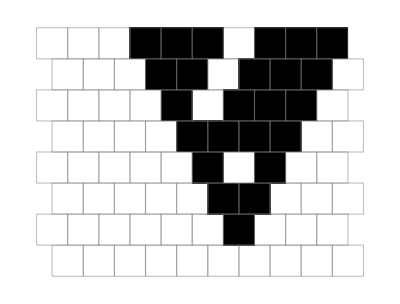
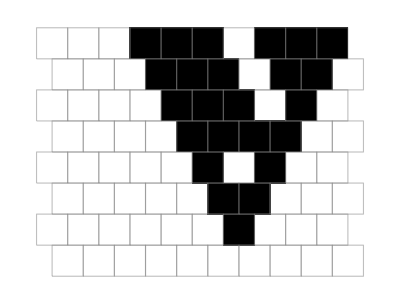
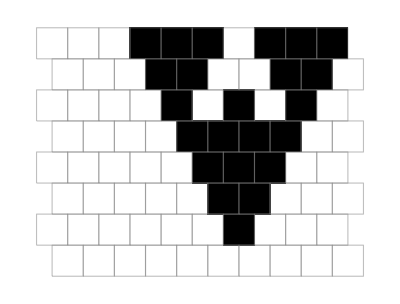
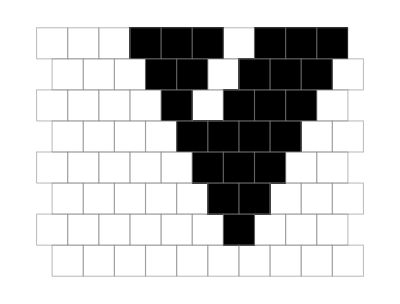
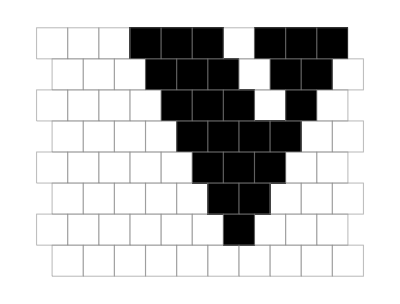
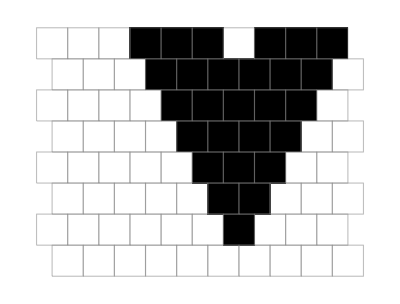
```mathematica
{-Graphics-,,,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}
```

## Functions and Parameters

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv", diffsmemo]
```

Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv

```mathematica
diffsmemo = {};
```

```mathematica
testlifetime = {{"[◼]", "TestLifetime"}}; randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
rulesmutationplot = {{"[◼]", "RulesMutationPlot"}}; customstyledata = {{"[◼]", "CustomStyleData"}};
```

```mathematica
k = 3; r = 1; initrule = {5586032021307, 3, 1}; trirule = {109636419052937157723438118980837975564,4,1};
longrule = {5600111605818,3,1};
initconditions = {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0};
nsteps = 12; initlifetime = testlifetime[initrule];
```

```mathematica
getca[rule_] := CellularAutomaton[rule, initconditions, nsteps]
```

```mathematica
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]] :=  Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

plot[ruleidx_Integer] := Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> {165, Automatic}
   ]]
```

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
 auto = getca[rules[[-1]]];
 mutes = Table[randomrulemutation[rules[[-1]]], 100];
 selected = Select[mutes,withinrange[#, 10, 12]&];
 Append[rules, TakeLargestBy[selected, getdiffs[rules, #]&, 1][[1]]]
]
```

## Cite This Notebook

“A Computational Model for Invasion Sports”
by Willem Nielsen
https://community.wolfram.com/groups/-/m/t/3210765?p_p_auth=mnG1KCWE